```mathematica
MyFunc[x_]:= Sin[Exp[Sqrt[x]]-Cos[Cos[Sin[Cos[Cos[-4.56501501314]]-Cos[Log[Sqrt[51.0596488845]]]]]]]*((Log[Exp[x]]+Sqrt[Abs[-32.191309277]]*x)*x)
```

```mathematica
DesiredFunc[x_]:=Sin[x*x]*(Abs[x]+5.3)+x
```

```mathematica
MyFunc2[x_]:=Sin [x*x]*((6.87203749639+Sin [Sin[(((6.87203749639+Abs[x])+Cos[-70.5529407735])/45.468748501)+Sin[x*x]]*x])+Sin[(Sin[Cos[-70.5529407735]]*Sin[Sin[(Sin[((Abs[x]*x + Sin[x])/45.468748501)+Sin[Abs[x]*x]]/(x*x))/45.468748501]*x])+Sin[Sin[x*x]*x]])

Plot[{MyFunc2[x],DesiredFunc[x]},{x, -2, 2.5}]
```

```mathematica
MyFunc3[x_]:= ((((x/Sin[Abs[x]])+(((Sin[Sin[Cos[Abs[x]]]]/-0.0956802175023502) + (Sin[Sin[Cos[Abs[x]]]]+5.472573221839978))+Sin[Sqrt[Sin[Sqrt[Sin[Sin[Sin[Sin[Cos[Abs[x]]]]]]]]]]))*Sin[Sin[Cos[Abs[x]]]])+(((0.971681104211586/Log[Sin[Cos[Sin[Abs[x]]]]])+(Sin[Sin[Cos[Abs[x]]]]+5.472573221839978))+Cos[x]))*Abs[x]

DesiredFunc[x_]:=Sin[x*x]*(Abs[x]+5.3)+x
```

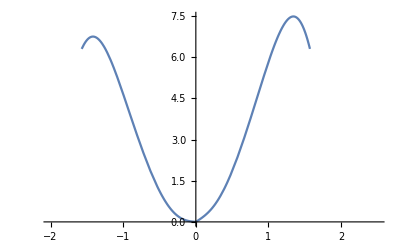

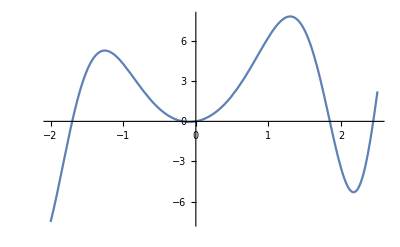

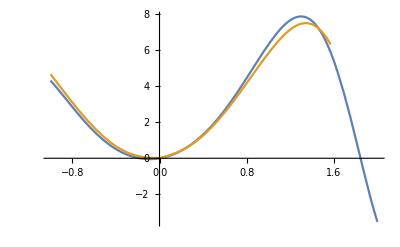

```mathematica
Plot[{MyFunc3[x]},{x,-2,2.5}]
Plot[{DesiredFunc[x]}, {x,-2,2.5}]
Plot[{DesiredFunc[x], MyFunc3[x]},{x,-1,2}]
```

```mathematica
MyFunc4[x_]:= ((((x/Sin[Sin[Sin[Sin[Sin[Sin[Abs[x]]]]]]])+(((Sin[Sin[Cos[x]]]/-0.0956802175023502)+(0.6779434738501462+5.472573221839978))+Sin[Sin[Sin[Sin[Abs[x]]]]]))*Sin[Sin[Sin[Sin[Sin[Cos[Abs[x]]]]]]])+(((Cos[Sin[Sin[Cos[x]]]]/Log[Sin[Cos[Sin[Abs[x]]]]])+(Sin[Sin[Sin[Sin[Sin[Sin[Sin[Cos[Abs[x]]]]]]]]]+5.472573221839978))+Sin[Sin[Sin[Sin[Sin[Sin[Cos[x]]]]]]]))*Abs[x]
```

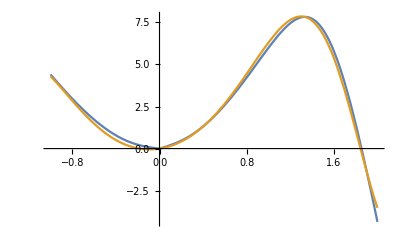

```mathematica
Plot[{MyFunc4[x], DesiredFunc[x]},{x,-1,2}]
```